```mathematica
(****
TEMPLATE FOR ITERATIVE OPTIMIZATION ALGORITHMS
Zicheng Gao
 ****)
```

```mathematica
(*** Iteration Settings ***)
InitIterationSettings[]:=(
(* Controls - zero fps means that there is NO DELAY *)
doPrint=False;
doPoint=True;
doGraph=False;
doWarn=False;
doPlot=True;
doSpace=True;
doEPlot=False;

showMistakes=False;
fps=0;

(*Init*)
dir=gFunc@@iterParams;
err=eFunc@@iterParams;

(** Adaptivity **)
errorRatio=1.0;(*In what ratio of current error to previous error should it be considered increasing*)
boostRatio=1.1; (*'Impatience' Multiplier to increase factor when error is not increasing*)
refineRatio=0.95;(*'Caution' Multiplier to decrease factor when error is increasing*)
maxRefines=1000;(*Give up refining if refined too many times in a row*)
(* Acceleration *)
AccelBoost=1.;
AccelRefine=1.;
AccelAmt=0.01;

(* Tracker values *)
historyAmt=300;

(*Display*)
dispGradientRange=1.;
);
InitIterationSettings[];
```

```mathematica
InitFunctionData[paramVariance_,manualTrueParams_,noiseFactor_, noiseDistribution_,forceData_]:=(
Clear[eFunc,gFunc,params];
ParamVariance=paramVariance;

(*If we are forcing data, use data, otherwise generate data*)
If[Length[forceData]>0,
Data=forceData;
DataLength=Length[Data];
SamplingSet=N[Range[DataLength]]/N[SamplingRate];
(* Else *),
SamplingSet=N[Range[DataLength]]/N[SamplingRate];
TrueParams=If[Length[manualTrueParams]>0,manualTrueParams,RandomReal[{-paramVariance,paramVariance},varamt]];
(* Data Generation *)
NoiselessData=((Fitfunction@@ #&)/@(Prepend[TrueParams, #]& /@SamplingSet));
AddNoise=(#+noiseFactor*RandomVariate[noiseDistribution])&;
Data=AddNoise/@NoiselessData;
];

(*Prep gradient*)
params=Table[Unique["p"],{varamt}];paramh=Hold@@params;

(* Objective and Gradient functions *)
eFunc=paramh/._[vars__]:>Function[{vars},N[Mean[(((Fitfunction@@Prepend[{vars},#])&/@SamplingSet)-Data)^2]]];
gFunc=paramh/._[vars__]:>Function[{vars},Evaluate@Grad[eFunc@@params,params]];
);
(*** Global Iteration Reset / Initialize ***)
InitIterationData[factorx_,manualParams_]:=(
totalIter=0;
TotalRefines=0;

(** Modification Values **)
factor=factorx;
dirs=ConstantArray[ConstantArray[0,varamt],Smoothness];
dirX=0;
err=-1;
prevErr=-2;
ConsecRefines=0;

(*History*)
iterParams=initParams=If[Length[manualParams]>0,manualParams,RandomReal[{-ParamVariance,ParamVariance},varamt]];
debugParams={iterParams};

err=eFunc@@iterParams;
dir=gFunc@@iterParams;
debugErr={err};
);
LinePlot[points_, size_,amount_]:=Show[
ListPointPlot3D[
{If[amount>0&&size>amount,points[[-amount;;-1]],points]},
PlotRange->All,ImageSize->Medium],
Graphics3D@Line@points
];
ReportIteration[i_]:=If[Mod[i,100]==0 && doPrint,Print["next dir:",dir,"\nerr:",err,"\nparams:",iterParams,"\niteration:",i];];
(* Realtime monitor plot *)
displayGradient[xV_,yV_]:=Show[
ContourPlot[eFunc @@ ReplacePart[iterParams, {xV->x,yV->y}],
{x,iterParams[[xV]]-dispGradientRange,iterParams[[xV]]+dispGradientRange},{y,iterParams[[yV]]-dispGradientRange,iterParams[[yV]]+dispGradientRange},
PlotTheme->"Web",AxesLabel->{x,y,z},PlotRange->All,ImageSize->Small,PerformanceGoal->"Speed"
],
Graphics[{
Blue,PointSize[0.05],Point[{iterParams[[xV]],iterParams[[yV]]}],
Arrow[{{iterParams[[xV]],iterParams[[yV]]},{iterParams[[xV]]-factor*dir[[xV]],iterParams[[yV]]-factor*dir[[yV]]}}]
}]
];
(* Realtime monitor plot *)
displayGradientNorm[xV_,yV_,ϵ_]:=Show[
ContourPlot[Norm[gFunc @@ ReplacePart[iterParams, {xV->x,yV->y}]],
{x,iterParams[[xV]]-dispGradientRange,iterParams[[xV]]+dispGradientRange},{y,iterParams[[yV]]-dispGradientRange,iterParams[[yV]]+dispGradientRange},
RegionFunction->Function[{x,y,z},z≤ϵ], PlotTheme->"Web",AxesLabel->{x,y,z},PlotRange->All,ImageSize->Small,PerformanceGoal->"Speed"
],
Graphics[{
Blue,PointSize[0.05],Point[{iterParams[[xV]],iterParams[[yV]]}],
Arrow[{{iterParams[[xV]],iterParams[[yV]]},{iterParams[[xV]]-factor*dir[[xV]],iterParams[[yV]]-factor*dir[[yV]]}}]
}]
];
Visualize[]:=Dynamic[Grid[{{"Data vs Function","Parameter Space","Error over iterations"},
{ListPlot[{(Fitfunction@@Prepend[iterParams,#])&/@SamplingSet,Data},Joined->True,ImageSize->Medium,PlotLegends->None]
,If[doPoint,If[varamt==3,If[doGraph,
{displayGradient[1,2],displayGradient[2,3],displayGradient[3,1]},
LinePlot[debugParams,totalIter,historyAmt]],
"Non-3 dimensions"],
"Disabled"],
If[doEPlot,ListLogPlot[debugErr,ImageSize->Medium,PlotRange->All],"Disabled"]
},
{"Parameters, nGrad, dir, Delta","Iterations, factor, corrections"},{Column[{iterParams,-dir,-factor*dir,-factor*SmoothingFunction[dirs]}],Column[{{totalIter,factor,TotalRefines},ProgressIndicator[ConsecRefines/maxRefines]}],{(Total[(((Fitfunction@@Prepend[iterParams,#])&/@SamplingSet)-Data)^2]/(DataLength-varamt))^0.5,prevErr}}
},Frame->All,ItemSize->30]];
RefineFactor[]:=(factor*=refineRatio^AccelRefine;ConsecRefines++;TotalRefines++;AccelRefine+=AccelAmt;AccelBoost=1.;);
BoostFactor[]:=(factor*=boostRatio^AccelBoost;prevErr=err;ConsecRefines=0;AccelBoost+=AccelAmt;AccelRefine=1.;);
AddToHistory[]:=(debugParams=Append[debugParams,iterParams];debugErr=Append[debugErr,err];);
ToSpacedString=Function[str,StringDrop[StringJoin@@((ToString[#]<>" ")&/@str),-1]];
FindMax[list_]:=Position[list,Max@list][[1,1]];
RecoverFrequency[data_,len_,rate_]:=N[(#-2+2(FindMax@Abs@Fourier[data*Exp[2I π(#-2)N@(Range@len-1)/len],FourierParameters->{0,2/len}]-1)/len)*2π*rate/len]&@FindMax@Abs@Fourier@data;
```

```mathematica
(* SET DATA *)
varamt=3;
DataLength=100;
SamplingRate=100;
Fitfunction=Exp[#1*#3]Sin[#1*#2]+#4&;
InitFunctionData[10.,{4.73575,9.87798,-8.94354},0.,NormalDistribution[],{}];
RecordedSmoothnessComparisonData={};
```

```mathematica
(* BEGIN ITERATION *)
InitIterationSettings[];
Smoothness=16;
SmoothingFunction[l_]:=Total[MapIndexed[#1 /2.^First[#2]&,l]]/Smoothness;
InitIterationData[0.01,{RecoverFrequency[Data,DataLength,SamplingRate],1.,0.629}];
recordAtIter=200;
Visualize[]
```

```mathematica
(*** Iteration loop ***)

(* Iterator and maximum values *)
i=0.;UpperBound=1000.;
SmallErr=0.0000000000000001;
NoErr=True;
Forever=False;
(* Iteration *)
While[ConsecRefines<maxRefines&&(Forever||(i<UpperBound &&(NoErr|| ((err(err-prevErr))^2+1)^2>(1+SmallErr)))),
(* Obtain vector from gradient and assign into running array *)
dirs=Prepend[Drop[dirs,-1],dir=gFunc@@iterParams];
ReportIteration[i];(*Report*)If[fps≠0&&ConsecRefines==0,Pause[fps];];(*Pause*)
If[showMistakes,AddToHistory[];];
(*Mark down boost vs error - please do not change other variables*)
iterParams-=factor*SmoothingFunction[dirs];
If[ConsecRefines==0,i++;totalIter++;];
err=eFunc @@ iterParams;
(* Factor Adaptivity - check to see whether error has increased over errorRatio to determine whether to boost or refine *)
If[err/prevErr>errorRatio,
(*If err increased, revert, refine, and retry*)
iterParams=debugParams[[-1]];If[Log10[factor]<-100,factor=0.5];
RefineFactor[];,AddToHistory[];BoostFactor[];];
]
```

$Aborted

```mathematica
(** Data Recording **)
RecordedSmoothnessComparisonData=Catenate[{
RecordedSmoothnessComparisonData,
{{{"Smoothness",Smoothness},debugErr,debugParams,TotalRefines}}
}];
```

Part::take: Cannot take positions -10 through -1 in {{0., 1., 0.629}}.

Function::fpct: Too many parameters in {p345, p346, p347} to be filled from Function[{p345, p346, p347}, N[Mean[((Apply[« 2 »] &)/@SamplingSet - Data)^2]]][{0., 1., 0.629}].

Function::fpct: Too many parameters in {p345, p346, p347} to be filled from Function[{p345, p346, p347}, N[Mean[((Apply[« 2 »] &)/@SamplingSet - Data)^2]]][-10, -1].

Part::pkspec1: The expression Function[{p345, p346, p347}, N[Mean[((Apply[« 2 »] &)/@SamplingSet - Data)^2]]][-10, -1] cannot be used as a part specification.

Part::take: Cannot take positions -10 through -1 in {{0., 1., 0.629}}.

Function::fpct: Too many parameters in {p345, p346, p347} to be filled from Function[{p345, p346, p347}, {0.01\ (0.02\ 2.71828^0.01\ p346\ Cos[0.01\ p345]\ (-3.6106 + p347 + Power[« 2 »]\ Sin[« 1 »]) + 0.04\ 2.71828^0.02\ p346\ Cos[0.02\ p345]\ (-3.61921 + p347 + Power[« 2 »]\ Sin[« 1 »]) + 0.06\ 2.71828^0.03\ p346\ Cos[0.03\ p345]\ (-3.62808 + p347 + Power[« 2 »]\ Sin[« 1 »]) + 0.08\ 2.71828^0.04\ p346\ Cos[0.04\ p345]\ (-3.63723 + p347 + Power[« 2 »]\ Sin[« 1 »]) + 0.1\ 2.71828^0.05\ p346\ Cos[0.05\ p345]\ (-3.64666 + p347 + Power[« 2 »]\ Sin[« 1 »]) + « 42 » + 0.96\ 2.71828^0.48\ p346\ Cos[0.48\ p345]\ (-4.41766 + p347 + Power[« 2 »]\ Sin[« 1 »]) + 0.98\ 2.71828^0.49\ p346\ Cos[0.49\ p345]\ (-4.44687 + p347 + Power[« 2 »]\ Sin[« 1 »]) + 1.\ 2.71828^0.5\ p346\ Cos[0.5\ p345]\ (-4.47674 + p347 + Power[« 2 »]\ Sin[« 1 »]) + « 50 »), 0.01\ (« 1 » + « 49 » + « 50 »), 0.01\ (2\ (« 1 ») + « 49 » + « 50 »)}][{« 1 »}].

Function::fpct: Too many parameters in {p345, p346, p347} to be filled from « 1 ».

Part::pkspec1: The expression « 1 » cannot be used as a part specification.

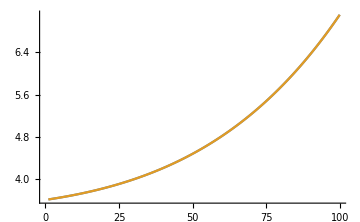

```mathematica
(***Diagnostic Tools***)

(*Parameter History*)
Grid[debugParams[[-10;;-1]]];
Column[eFunc @@ #&/@ debugParams[[-10;;-1]]];
Grid[gFunc @@ #&/@ debugParams[[-10;;-1]]];

(*"Best Parameters" Generated with NMinimize*)
AutoParams=params/.NMinimize[eFunc @@ params,params][[2]];

(*Compare current data, auto-fitted data, and generated data*)
ListPlot[{
(*(Fitfunction@@Prepend[iterParams,#])&/@SamplingSet,*)
(Fitfunction@@Prepend[AutoParams,#])&/@SamplingSet,
Data},Joined->True,ImageSize->Medium]
```

1.5

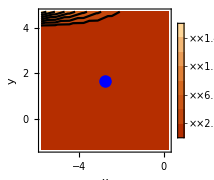
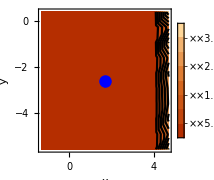
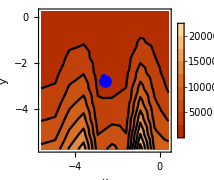

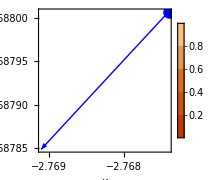
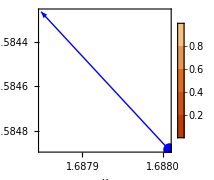
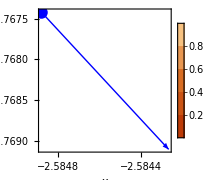

```mathematica
dispGradientRange=3.;
dispGradientThresh=1.5
{displayGradient[1,2],displayGradient[2,3],displayGradient[3,1]}
{displayGradientNorm[1,2,dispGradientThresh],displayGradientNorm[2,3,dispGradientThresh],displayGradientNorm[3,1,dispGradientThresh]}
```

```mathematica
LinePlot[debugParams,Length[debugParams],100]
```

-Graphics3D-

```mathematica
Last/@Table[RecordedSmoothnessComparisonData[[sm,2]],{sm,1,Length@RecordedSmoothnessComparisonData}]
(ListLogLogPlot[
Table[RecordedSmoothnessComparisonData[[sm,2]],{sm,1,Length@RecordedSmoothnessComparisonData}],PlotLegends->SwatchLegend[
Table[
Column[{
ToSpacedString@RecordedSmoothnessComparisonData[[sm,1]],
ToSpacedString@{"Final error:",Last@RecordedSmoothnessComparisonData[[sm,2]]}}
],
{sm,1,Length@RecordedSmoothnessComparisonData}
],
LegendFunction->"Panel"],
PlotLabel->"Inverse power of two gradient smoothing function with various length amounts",
AxesLabel->{"Iterations","Error"},
ImageSize->Large,
Joined->True])
```

{}

ListLogLogPlot::argx: ListLogLogPlot called with 0 arguments; 1 argument is expected.

General::stop: Further output of ListLogLogPlot :: argx will be suppressed during this calculation.

ListLogLogPlot[{},PlotLegends→SwatchLegend[{},LegendFunction→Panel],PlotLabel→Inverse power of two gradient smoothing function with various length amounts,AxesLabel→{Iterations,Error},ImageSize→Large,Joined→True]

```mathematica
ListPlot[
Table[{RecordedSmoothnessComparisonData[[sm,1,1]],RecordedSmoothnessComparisonData[[sm,4]]/1000.},{sm,1,Length@RecordedSmoothnessComparisonData}],
AxesLabel->{"Length of smoothing function","Corrections / Iterations"},
PlotLabel->"Correction Amounts of P2 Smoothing Function with various length amounts",
ImageSize->Large
]
```

-Graphics-

```mathematica
Data
TrueParams
```

{-8.89128,-8.82831,-8.7531,-8.664,-8.55913,-8.43646,-8.29371,-8.12839,-7.93777,-7.71885,-7.46833,-7.18265,-6.85792,-6.48989,-6.074,-5.6053,-5.07847,-4.4878,-3.82717,-3.09005,-2.26951,-1.35821,-0.348391,0.768073,1.99968,3.35526,4.84391,6.47498,8.25796,10.2024,12.3178,14.6134,17.0982,19.7806,22.6682,25.7675,29.0837,32.6202,36.3783,40.3565,44.5503,48.951,53.5456,58.3155,63.2359,68.2742,73.3896,78.5311,83.6362,88.6292,93.4196,97.8996,101.942,105.398,108.093,109.825,110.361,109.434,106.735,101.913,94.5679,84.2471,70.4366,52.5576,29.958,1.90662,-32.4158,-73.924,-123.637,-182.689,-252.337,-333.971,-429.128,-539.5,-666.949,-813.514,-981.429,-1173.13,-1391.27,-1638.74,-1918.67,-2234.42,-2589.64,-2988.25,-3434.43,-3932.67,-4487.74,-5104.67,-5788.83,-6545.81,-7381.49,-8301.98,-9313.62,-10422.9,-11636.4,-12960.9,-14403.1,-15969.4,-17666.3,-19499.9}

{4.73575,9.87798,-8.94354}